```mathematica
α=2.;u0=1.*10^-8;
V[r_]=-1/r-(1.0415223038416566 ⅇ^(-0.9990999998788636 r))/r;
k:=√(2e);SPS1={};SPS2={};SPS3={};SPS4={};SPS5={};SPS6={};SPS7={};
```

```mathematica
r2=u0;
```

```mathematica
Print["     ","δ(0.01)→-0.654835316","            ","δ(0.03)→1.232867297","            ","δ(0.07)→-0.579619620","            ","δ(0.1)→-1.156444634","            ","δ(0.3)→-0.106466466","            ","δ(0.7)→-1.457426179","            ","δ(1)→1.160634967","    "];
Table[
e=0.01;
sol1=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-1.3},WorkingPrecision->20];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[SPS1,{r1,δ1}];
e=0.03;
sol2=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,0.9},WorkingPrecision->20];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
AppendTo[SPS2,{r1,δ2}];
e=0.07;
sol3=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs3=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol3,{δ,-0.2},WorkingPrecision->20];
δ3=δ/.δs3;
δ3=NestWhile[Sign[#](Abs[#]-π)&,δ3,Abs[#]>π/2&];
AppendTo[SPS3,{r1,δ3}];
e=0.1;
sol4=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs4=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol4,{δ,-0.6},WorkingPrecision->20];
δ4=δ/.δs4;
δ4=NestWhile[Sign[#](Abs[#]-π)&,δ4,Abs[#]>π/2&];
AppendTo[SPS4,{r1,δ4}];
e=0.3;
sol5=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs5=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol5,{δ,1.2},WorkingPrecision->20];
δ5=δ/.δs5;
δ5=NestWhile[Sign[#](Abs[#]-π)&,δ5,Abs[#]>π/2&];
AppendTo[SPS5,{r1,δ5}];
e=0.7;
sol6=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs6=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol6,{δ,-0.6},WorkingPrecision->20];
δ6=δ/.δs6;
δ6=NestWhile[Sign[#](Abs[#]-π)&,δ6,Abs[#]>π/2&];
AppendTo[SPS6,{r1,δ6}];
e=1;
sol7=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs7=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol7,{δ,-1.1},WorkingPrecision->20];
δ7=δ/.δs7;
δ7=NestWhile[Sign[#](Abs[#]-π)&,δ7,Abs[#]>π/2&];
AppendTo[SPS7,{r1,δ7}];
Print[r1" ","δ(0.01)→"Style[δ1,If[Abs[δ1+0.65]<0.3,Red,Black]],"  ","δ(0.03)→"Style[δ2,If[Abs[δ2-1.23]<0.3,Red,Black]],"  ","δ(0.07)→"Style[δ3,If[Abs[δ3+0.58]<0.3,Red,Black]],"  ","δ(0.1)→"Style[δ4,If[Abs[δ4+1.15]<0.3,Red,Black]],"  ","δ(0.3)→"Style[δ5,If[Abs[δ5+0.1]<0.3,Red,Black]],"  ","δ(0.7)→"Style[δ6,If[Abs[δ6+1.45]<0.3,Red,Black]],"  ","δ(1)→"Style[δ7,If[Abs[δ7-1.15]<0.3,Red,Black]],"  "],{r1,1,200,1}]
```

δ(0.01)→-0.654835316            δ(0.03)→1.232867297            δ(0.07)→-0.579619620            δ(0.1)→-1.156444634            δ(0.3)→-0.106466466            δ(0.7)→-1.457426179            δ(1)→1.160634967

NDSolve::precw: 参数函数的精度 ({{2. (0.01+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (-22.3597387221049468655600380205778387952583462604==-7.21249 Cot[8.78838-δ]) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.03+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (-24.8920321955034723863552138352025996547322042021==-4.32743 Cot[2.66814-δ]) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.07+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (-31.940492492497650718714359890964993212470964776==-3.04678 Cot[0.400649-δ]) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

δ(0.01)→ (-0.94842882085366896039)  δ(0.03)→ (-0.645580318093936933)  δ(0.07)→ 0.30554786215034924911  δ(0.1)→ (-0.26432244061558843953)  δ(0.3)→ (-1.309741504176627378)  δ(0.7)→ 1.39024107294914802  δ(1)→ 1.243009918919108738

2  δ(0.01)→ (-1.1160774390156484518)  δ(0.03)→ 0.93687658910478731775  δ(0.07)→ (-0.52861327221746070091)  δ(0.1)→ (-0.89937399398788832183)  δ(0.3)→ (-1.563322825239369836)  δ(0.7)→ 1.313003256106396805  δ(1)→ 1.225215103137698558

3  δ(0.01)→ (-0.66425418579492111146)  δ(0.03)→ (-0.4349347895408066599)  δ(0.07)→ (-1.2345478254537224621)  δ(0.1)→ (-1.3929786871192593049)  δ(0.3)→ 1.5084349367859009265  δ(0.7)→ 1.332273691181821597  δ(1)→ 1.234983443382387712

4  δ(0.01)→ 1.1044240013091441465  δ(0.03)→ (-0.8847375130158949817)  δ(0.07)→ (-1.34363950523059461)  δ(0.1)→ (-1.4341587885107655769)  δ(0.3)→ 1.4925414594349240812  δ(0.7)→ 1.298177286881489787  δ(1)→ 1.220409880199368581

5  δ(0.01)→ 0.8071619354825888378  δ(0.03)→ (-1.0144277178925133227)  δ(0.07)→ (-1.4516846603403490278)  δ(0.1)→ (-1.5416002603215020771)  δ(0.3)→ 1.4163047966177893046  δ(0.7)→ 1.29714354614557885  δ(1)→ 1.219655383502999604

6  δ(0.01)→ (-0.1556666332442772164)  δ(0.03)→ (-1.466882420948539769)  δ(0.07)→ 1.437217600503850528  δ(0.1)→ 1.409016268607837362  δ(0.3)→ 1.3950954536815648724  δ(0.7)→ 1.285549096607488519  δ(1)→ 1.210519197713103055

7  δ(0.01)→ (-1.1138391945840410842)  δ(0.03)→ 1.2223939308691397125  δ(0.07)→ 1.2399556363677671917  δ(0.1)→ 1.2967597132654606185  δ(0.3)→ 1.3930263722797094098  δ(0.7)→ 1.2778984496140183396  δ(1)→ 1.210203240169982562

8  δ(0.01)→ 1.241614293343372362  δ(0.03)→ 0.92205840353055250464  δ(0.07)→ 1.1768216795708698172  δ(0.1)→ 1.2839477669849461447  δ(0.3)→ 1.3638489641544914963  δ(0.7)→ 1.276776799489291198  δ(1)→ 1.20442166707739553

9  δ(0.01)→ 0.74256084956980962362  δ(0.03)→ 0.83257446760895487738  δ(0.07)→ 1.175475385863952709  δ(0.1)→ 1.270066707560870574  δ(0.3)→ 1.345948210186375758  δ(0.7)→ 1.2686092231946101608  δ(1)→ 1.204556697025726649

10  δ(0.01)→ 0.639333176742429297  δ(0.03)→ 0.82250896057321138087  δ(0.07)→ 1.125643797615288542  δ(0.1)→ 1.208309444561251167  δ(0.3)→ 1.34680651253883593  δ(0.7)→ 1.26894610069760209  δ(1)→ 1.200604810571615557

11  δ(0.01)→ 0.530670552167316819  δ(0.03)→ 0.71711946521803763526  δ(0.07)→ 1.0310773774685122948  δ(0.1)→ 1.1388499789485070791  δ(0.3)→ 1.3376055748587360908  δ(0.7)→ 1.264554876362780425  δ(1)→ 1.200850440922071408

12  δ(0.01)→ 0.187988703537278582  δ(0.03)→ 0.53534049322697957168  δ(0.07)→ 0.94525321045558640831  δ(0.1)→ 1.1028984409347635281  δ(0.3)→ 1.3228723912526075471  δ(0.7)→ 1.2624657051101866178  δ(1)→ 1.198070416505836355

13  δ(0.01)→ (-0.23561038404339190751)  δ(0.03)→ 0.34820418306194229648  δ(0.07)→ 0.90349469062509133552  δ(0.1)→ 1.0996664672022048079  δ(0.3)→ 1.3197086810214333889  δ(0.7)→ 1.261862874143528472  δ(1)→ 1.198208668689346935

14  δ(0.01)→ (-0.64809338090696910315)  δ(0.03)→ 0.20766902218219667819  δ(0.07)→ 0.89923009498002938377  δ(0.1)→ 1.095091710909561411  δ(0.3)→ 1.3191871186023999791  δ(0.7)→ 1.2585209650769107216  δ(1)→ 1.196295358081047345

15  δ(0.01)→ (-0.99878654309264749259)  δ(0.03)→ 0.141028146723053726  δ(0.07)→ 0.8941718047530273759  δ(0.1)→ 1.069216358743523719  δ(0.3)→ 1.3109803858374716631  δ(0.7)→ 1.25867699795217164  δ(1)→ 1.19621882718206894

16  δ(0.01)→ (-1.2408304852491676765)  δ(0.03)→ 0.132275889244138481  δ(0.07)→ 0.8640001844558124572  δ(0.1)→ 1.033478502417514581  δ(0.3)→ 1.3041793985496128376  δ(0.7)→ 1.256705082959132656  δ(1)→ 1.194988065147373629

17  δ(0.01)→ (-1.338101053284785465)  δ(0.03)→ 0.12391036306682776532  δ(0.07)→ 0.81702549391764816455  δ(0.1)→ 1.0084458525728198457  δ(0.3)→ 1.3040697639877101454  δ(0.7)→ 1.2555145311079250855  δ(1)→ 1.194672256706259034

18  δ(0.01)→ (-1.3449169010528386575)  δ(0.03)→ 0.075312193045363145593  δ(0.07)→ 0.77503700438490913481  δ(0.1)→ 1.0016404001071101163  δ(0.3)→ 1.302221754007926067  δ(0.7)→ 1.255353750479430901  δ(1)→ 1.193973175155336154

19  δ(0.01)→ (-1.4008685138992474864)  δ(0.03)→ (-0.0092798799655131825862)  δ(0.07)→ 0.75324737109369855852  δ(0.1)→ 1.00206018239966821  δ(0.3)→ 1.2962200361294982337  δ(0.7)→ 1.25350023884331758  δ(1)→ 1.1934540567527234262

20  δ(0.01)→ (-1.551476077567410104)  δ(0.03)→ (-0.10543154468503689929)  δ(0.07)→ 0.74988716373502531381  δ(0.1)→ 0.9945309854606687778  δ(0.3)→ 1.2931177656211707017  δ(0.7)→ 1.253499256305216487  δ(1)→ 1.193140725205420312

21  δ(0.01)→ 1.381866819148529653  δ(0.03)→ (-0.18867479872548771967)  δ(0.07)→ 0.7491066067782245648  δ(0.1)→ 0.9762886846664654065  δ(0.3)→ 1.29340146761762714  δ(0.7)→ 1.25255456200244333  δ(1)→ 1.1924932542458678562

22  δ(0.01)→ 1.156060310732191608  δ(0.03)→ (-0.242051744818514664)  δ(0.07)→ 0.7368937722425765676  δ(0.1)→ 0.95651003897129722107  δ(0.3)→ 1.2911493526629979052  δ(0.7)→ 1.2516365941836223889  δ(1)→ 1.192422463361482073

23  δ(0.01)→ 0.9416160968043747001  δ(0.03)→ (-0.26217030418927799)  δ(0.07)→ 0.71257932073011919415  δ(0.1)→ 0.94499030911919664874  δ(0.3)→ 1.286960099075173431  δ(0.7)→ 1.25166841248829273  δ(1)→ 1.191738672483205974

24  δ(0.01)→ 0.761677870213466268  δ(0.03)→ (-0.26324814520655855)  δ(0.07)→ 0.68573029476150091939  δ(0.1)→ 0.9429485682217299761  δ(0.3)→ 1.28557071957595255  δ(0.7)→ 1.25051922666297266  δ(1)→ 1.191779236262347665

25  δ(0.01)→ 0.63653886810831132541  δ(0.03)→ (-0.26878312261443149914)  δ(0.07)→ 0.66685434533369717768  δ(0.1)→ 0.9428735374813258458  δ(0.3)→ 1.2856981308605275598  δ(0.7)→ 1.2503824581472642387  δ(1)→ 1.191147348868850927

26  δ(0.01)→ 0.5771591268887345583  δ(0.03)→ (-0.29410419698751168766)  δ(0.07)→ 0.65990184130248451923  δ(0.1)→ 0.9370448995522514102  δ(0.3)→ 1.2834980785550836625  δ(0.7)→ 1.24996271997683115  δ(1)→ 1.191192636410325317

27  δ(0.01)→ 0.567472689603879491  δ(0.03)→ (-0.33908436905617349125)  δ(0.07)→ 0.65991366758181108846  δ(0.1)→ 0.9250034925991471027  δ(0.3)→ 1.2805925456671215899  δ(0.7)→ 1.2491954149916878744  δ(1)→ 1.19067992364811485

28  δ(0.01)→ 0.560987959425443171  δ(0.03)→ (-0.39370988520784993224)  δ(0.07)→ 0.6576671150642267415  δ(0.1)→ 0.91254701390178980168  δ(0.3)→ 1.2800043160739636908  δ(0.7)→ 1.249269794769333101  δ(1)→ 1.190658114731218724

29  δ(0.01)→ 0.5174221459815063207  δ(0.03)→ (-0.44544208025348179999)  δ(0.07)→ 0.64755772757205626168  δ(0.1)→ 0.90543222039110786511  δ(0.3)→ 1.2799239192269187128  δ(0.7)→ 1.248555639261409178  δ(1)→ 1.19030009115122736

30  δ(0.01)→ 0.4294898930657217786  δ(0.03)→ (-0.4839215860245934494)  δ(0.07)→ 0.63115825143162107769  δ(0.1)→ 0.90419705002112321551  δ(0.3)→ 1.2779452202353143216  δ(0.7)→ 1.2483079406662518545  δ(1)→ 1.1901787077368890784

31  δ(0.01)→ 0.310432926471972456  δ(0.03)→ (-0.504287542485090299)  δ(0.07)→ 0.61464024645501189619  δ(0.1)→ 0.9041852497685056474  δ(0.3)→ 1.275915598839079275  δ(0.7)→ 1.24817016662949846  δ(1)→ 1.189976167296528631

32  δ(0.01)→ 0.177392599682547346  δ(0.03)→ (-0.509504594109875595)  δ(0.07)→ 0.6038158873468682411  δ(0.1)→ 0.9004742777046368479  δ(0.3)→ 1.2757021048500808216  δ(0.7)→ 1.247538693846308123  δ(1)→ 1.189759493371109005

33  δ(0.01)→ 0.045663800460183483587  δ(0.03)→ (-0.5093901223969868478)  δ(0.07)→ 0.60023185564989662696  δ(0.1)→ 0.8924536761821366165  δ(0.3)→ 1.2754657995215856762  δ(0.7)→ 1.2475721161467761  δ(1)→ 1.189683274678193678

34  δ(0.01)→ (-0.071636906533064472641)  δ(0.03)→ (-0.51502534689285027841)  δ(0.07)→ 0.60038241741343117217  δ(0.1)→ 0.88369512527747150252  δ(0.3)→ 1.2737483294869020361  δ(0.7)→ 1.247162207592158011  δ(1)→ 1.189403275261653636

35  δ(0.01)→ (-0.16333447452092739931)  δ(0.03)→ (-0.53253090578178564078)  δ(0.07)→ 0.5986782159029648239  δ(0.1)→ 0.87822427810963943835  δ(0.3)→ 1.2723134566666147625  δ(0.7)→ 1.2468417945943043751  δ(1)→ 1.189404992160881602

36  δ(0.01)→ (-0.22170817831223469078)  δ(0.03)→ (-0.56116786812922033286)  δ(0.07)→ 0.59179662977334613848  δ(0.1)→ 0.87693902281139796189  δ(0.3)→ 1.2722711399649461085  δ(0.7)→ 1.246839365179553388  δ(1)→ 1.189107984399728831

37  δ(0.01)→ (-0.24669863562651503587)  δ(0.03)→ (-0.59547063992635942529)  δ(0.07)→ 0.58070209532321345333  δ(0.1)→ 0.877081378071612796  δ(0.3)→ 1.27193740827564236  δ(0.7)→ 1.246352543036119612  δ(1)→ 1.189133737338741171

38  δ(0.01)→ (-0.250190809548779808)  δ(0.03)→ (-0.6283661006462892104)  δ(0.07)→ 0.5693076014925475759  δ(0.1)→ 0.8750639650517412021  δ(0.3)→ 1.2704691117684140033  δ(0.7)→ 1.246307287983808485  δ(1)→ 1.188866022448806434

39  δ(0.01)→ (-0.253067679700750851)  δ(0.03)→ (-0.6537384780579062093)  δ(0.07)→ 0.56150418800249220494  δ(0.1)→ 0.8697804243057560031  δ(0.3)→ 1.2694408282903874472  δ(0.7)→ 1.246111473222073747  δ(1)→ 1.18886962866777725

40  δ(0.01)→ (-0.273599895713731769)  δ(0.03)→ (-0.6683967320455421628)  δ(0.07)→ 0.55860040165558723047  δ(0.1)→ 0.86325747465509327841  δ(0.3)→ 1.2694713478653118824  δ(0.7)→ 1.2457659144812747742  δ(1)→ 1.188665384098215702

41  δ(0.01)→ (-0.318803272046513209)  δ(0.03)→ (-0.6733219417920668048)  δ(0.07)→ 0.55860507481511442761  δ(0.1)→ 0.85852447727296166041  δ(0.3)→ 1.2690851144431305084  δ(0.7)→ 1.245801430516101544  δ(1)→ 1.1886180480969919049

42  δ(0.01)→ (-0.38568599584494955111)  δ(0.03)→ (-0.6733864132670806)  δ(0.07)→ 0.5578360814211740764  δ(0.1)→ 0.85691038484344688038  δ(0.3)→ 1.2678362934260664588  δ(0.7)→ 1.245463717769925021  δ(1)→ 1.188492025148148749

43  δ(0.01)→ (-0.46654626362246965882)  δ(0.03)→ (-0.67503715447739446295)  δ(0.07)→ 0.55365289718991574381  δ(0.1)→ 0.857023164487070908  δ(0.3)→ 1.2670890952000931218  δ(0.7)→ 1.2453366573921203677  δ(1)→ 1.1883864848670469409

44  δ(0.01)→ (-0.55265394021323310632)  δ(0.03)→ (-0.68312292026079768427)  δ(0.07)→ 0.54613937243522227588  δ(0.1)→ 0.8561844454975546524  δ(0.3)→ 1.267145068227958095  δ(0.7)→ 1.245277592470910876  δ(1)→ 1.188332703420759486

45  δ(0.01)→ (-0.63572192653785445141)  δ(0.03)→ (-0.69897637484643423614)  δ(0.07)→ 0.53769376385354982447  δ(0.1)→ 0.852898893573950917  δ(0.3)→ 1.266736972500470197  δ(0.7)→ 1.2449546099926825315  δ(1)→ 1.188181437671052534

46  δ(0.01)→ (-0.70836987399634391702)  δ(0.03)→ (-0.7205614277163853754)  δ(0.07)→ 0.53121533402953401314  δ(0.1)→ 0.84802177736738740514  δ(0.3)→ 1.2656746728393726306  δ(0.7)→ 1.24496650876581254  δ(1)→ 1.188177481322635399

47  δ(0.01)→ (-0.76460024398921213845)  δ(0.03)→ (-0.743868507660497449)  δ(0.07)→ 0.52820076617520883965  δ(0.1)→ 0.84377871844621291532  δ(0.3)→ 1.2651242711917240172  δ(0.7)→ 1.244767206864023367  δ(1)→ 1.188006094233780117

48  δ(0.01)→ (-0.80087890460665830564)  δ(0.03)→ (-0.7645419262578819385)  δ(0.07)→ 0.52785422588882462602  δ(0.1)→ 0.84175628599965372279  δ(0.3)→ 1.26518345385318189  δ(0.7)→ 1.2445800619605880735  δ(1)→ 1.188021239362373308

49  δ(0.01)→ (-0.817823965479366734)  δ(0.03)→ (-0.7792978188555979808)  δ(0.07)→ 0.527751071075859553  δ(0.1)→ 0.8415988063608317978  δ(0.3)→ 1.2647731515203736518  δ(0.7)→ 1.244588919318115501  δ(1)→ 1.187859280068825733

50  δ(0.01)→ (-0.82141060324232545698)  δ(0.03)→ (-0.7869899145901957212)  δ(0.07)→ 0.5255910425468660903  δ(0.1)→ 0.841445498681296488  δ(0.3)→ 1.263866747940313107  δ(0.7)→ 1.244326486894729417  δ(1)→ 1.187863861409936977

51  δ(0.01)→ (-0.821774103896940679)  δ(0.03)→ (-0.789051326911773267)  δ(0.07)→ 0.52071998449421912555  δ(0.1)→ 0.8396492090309740878  δ(0.3)→ 1.2634559121545201422  δ(0.7)→ 1.2442847271791055453  δ(1)→ 1.187735801429213202

52  δ(0.01)→ (-0.8292231292610044174)  δ(0.03)→ (-0.78894063575731353)  δ(0.07)→ 0.51437783698563860753  δ(0.1)→ 0.8361663638175858996  δ(0.3)→ 1.2635085715214843007  δ(0.7)→ 1.244196506331582549  δ(1)→ 1.1877091506689973426

53  δ(0.01)→ (-0.85020300580904267463)  δ(0.03)→ (-0.79063312373848590942)  δ(0.07)→ 0.50871586380762444856  δ(0.1)→ 0.83244285634521264984  δ(0.3)→ 1.2631080765110964387  δ(0.7)→ 1.2439848342913490603  δ(1)→ 1.187627924924884237

54  δ(0.01)→ (-0.88603851447277579513)  δ(0.03)→ (-0.79692076832481605276)  δ(0.07)→ 0.50536751931485106175  δ(0.1)→ 0.83007585983429093881  δ(0.3)→ 1.2623310554885422958  δ(0.7)→ 1.244005487493626868  δ(1)→ 1.1875628677900540363

55  δ(0.01)→ (-0.93419279083121336925)  δ(0.03)→ (-0.8084553628825353556)  δ(0.07)→ 0.50444460534918039095  δ(0.1)→ 0.82946503162487533432  δ(0.3)→ 1.2620204425071572412  δ(0.7)→ 1.243824376674006847  δ(1)→ 1.187527471331786907

56  δ(0.01)→ (-0.99014123783704779585)  δ(0.03)→ (-0.82383911405107105265)  δ(0.07)→ 0.504543718595976434  δ(0.1)→ 0.8295488045569933221  δ(0.3)→ 1.2620630441301436134  δ(0.7)→ 1.2437262337434409104  δ(1)→ 1.187430503587450465

57  δ(0.01)→ (-1.0487204113438268495)  δ(0.03)→ (-0.8404089272526024667)  δ(0.07)→ 0.5037513713707708616  δ(0.1)→ 0.8287987244840210119  δ(0.3)→ 1.2616792883028396496  δ(0.7)→ 1.243710061697765839  δ(1)→ 1.187427863985402339

58  δ(0.01)→ (-1.1048591132289858529)  δ(0.03)→ (-0.855237304906310359)  δ(0.07)→ 0.50093014441292755031  δ(0.1)→ 0.8265478676970681378  δ(0.3)→ 1.2610094481709417298  δ(0.7)→ 1.243511512906307248  δ(1)→ 1.187315414076002216

59  δ(0.01)→ (-1.1540026601870753213)  δ(0.03)→ (-0.8660658187721132959)  δ(0.07)→ 0.49638020944150328201  δ(0.1)→ 0.82347942057200117962  δ(0.3)→ 1.2607716653228250743  δ(0.7)→ 1.2435061386398603  δ(1)→ 1.18732555380977363

60  δ(0.01)→ (-1.1925432839841657981)  δ(0.03)→ (-0.8720137567353648999)  δ(0.07)→ 0.49151881322752786123  δ(0.1)→ 0.82095125473962862072  δ(0.3)→ 1.260803671845159801  δ(0.7)→ 1.243407049199817218  δ(1)→ 1.187217818679350215

61  δ(0.01)→ (-1.2184358119911482303)  δ(0.03)→ (-0.8738787710756577807)  δ(0.07)→ 0.48791051157554206347  δ(0.1)→ 0.81982470000835776719  δ(0.3)→ 1.2604402947042970527  δ(0.7)→ 1.2432700495249724049  δ(1)→ 1.18722045829064961

62  δ(0.01)→ (-1.2319382111102323984)  δ(0.03)→ (-0.873841372427988589)  δ(0.07)→ 0.4862870432756154451  δ(0.1)→ 0.81977725525811428371  δ(0.3)→ 1.2598593457930612188  δ(0.7)→ 1.24328386239078527  δ(1)→ 1.187134838752729779

63  δ(0.01)→ (-1.2360676128881120251)  δ(0.03)→ (-0.87459622265573420318)  δ(0.07)→ 0.48612944920186761268  δ(0.1)→ 0.8196384249833271515  δ(0.3)→ 1.259675082314569781  δ(0.7)→ 1.243127787198184522  δ(1)→ 1.1871153925546457422

64  δ(0.01)→ (-1.236157782687755577)  δ(0.03)→ (-0.87828667099439966445)  δ(0.07)→ 0.486058498436735574  δ(0.1)→ 0.8184229540876464901  δ(0.3)→ 1.2596973190517251473  δ(0.7)→ 1.2430798915630159865  δ(1)→ 1.187061478723202727

65  δ(0.01)→ (-1.2383102317191688781)  δ(0.03)→ (-0.8857622006481521585)  δ(0.07)→ 0.4847663228391099388  δ(0.1)→ 0.8161387793595624963  δ(0.3)→ 1.2593558707848560173  δ(0.7)→ 1.243045856059780626  δ(1)→ 1.187014719386229219

66  δ(0.01)→ (-1.2474461235545548601)  δ(0.03)→ (-0.89643652884239872122)  δ(0.07)→ 0.48184136577825296871  δ(0.1)→ 0.81370782984649692833  δ(0.3)→ 1.2588488582638965385  δ(0.7)→ 1.2428980404702129992  δ(1)→ 1.186992156786698145

67  δ(0.01)→ (-1.266062151125412954)  δ(0.03)→ (-0.9086600776044712779)  δ(0.07)→ 0.47795428074044181601  δ(0.1)→ 0.81214704578156996048  δ(0.3)→ 1.2587043364765801611  δ(0.7)→ 1.24290612375059648  δ(1)→ 1.186922704007757287

68  δ(0.01)→ (-1.2941378537875099513)  δ(0.03)→ (-0.9203509143453188704)  δ(0.07)→ 0.47436202177055056215  δ(0.1)→ 0.81172687981481389413  δ(0.3)→ 1.2587181618985579005  δ(0.7)→ 1.24280679552656998  δ(1)→ 1.186922289330196535

69  δ(0.01)→ (-1.3297953142823925036)  δ(0.03)→ (-0.9296639180133258963)  δ(0.07)→ 0.4721011985500001726  δ(0.1)→ 0.811786078863382995  δ(0.3)→ 1.2583988961924809505  δ(0.7)→ 1.2427197863077376194  δ(1)→ 1.186842074124011514

70  δ(0.01)→ (-1.3701097481989622769)  δ(0.03)→ (-0.9355525577109309463)  δ(0.07)→ 0.47136256329671714726  δ(0.1)→ 0.8113292731493589405  δ(0.3)→ 1.2579536231491846636  δ(0.7)→ 1.242722976412295449  δ(1)→ 1.186849442279180466

71  δ(0.01)→ (-1.4117473970822513489)  δ(0.03)→ (-0.9380958728078266615)  δ(0.07)→ 0.47140952965717610202  δ(0.1)→ 0.8098710653988884143  δ(0.3)→ 1.2578389008121458344  δ(0.7)→ 1.242592425569794117  δ(1)→ 1.186773200993880622

72  δ(0.01)→ (-1.4513972571331432705)  δ(0.03)→ (-0.9384657769449877009)  δ(0.07)→ 0.4710828873031884067  δ(0.1)→ 0.807802083337363481  δ(0.3)→ 1.2578457939558863394  δ(0.7)→ 1.2425725703180797872  δ(1)→ 1.186773735424323795

73  δ(0.01)→ (-1.486093407258539178)  δ(0.03)→ (-0.938494948021242141)  δ(0.07)→ 0.46955120882491414687  δ(0.1)→ 0.80601340245853051766  δ(0.3)→ 1.2575481849095822161  δ(0.7)→ 1.242527447643184624  δ(1)→ 1.186714090250616288

74  δ(0.01)→ (-1.5135351998723549729)  δ(0.03)→ (-0.93999136237545306298)  δ(0.07)→ 0.46680534200690537632  δ(0.1)→ 0.80514143592943028199  δ(0.3)→ 1.257154700827265955  δ(0.7)→ 1.2424188360972336069  δ(1)→ 1.1866974497605507462

75  δ(0.01)→ (-1.5324575365037368253)  δ(0.03)→ (-0.94409783301565707238)  δ(0.07)→ 0.46360629161804776723  δ(0.1)→ 0.8050603325795228342  δ(0.3)→ 1.2570625246641452733  δ(0.7)→ 1.242429578772571963  δ(1)→ 1.186661115637131722

76  δ(0.01)→ (-1.5429997853571388124)  δ(0.03)→ (-0.95096149149539290713)  δ(0.07)→ 0.46097384000046861037  δ(0.1)→ 0.805021121702749316  δ(0.3)→ 1.2570638906164947815  δ(0.7)→ 1.242335755133345534  δ(1)→ 1.1866240064968629982

77  δ(0.01)→ (-1.5468953671129943933)  δ(0.03)→ (-0.9597883938786975175)  δ(0.07)→ 0.45955561158053907096  δ(0.1)→ 0.8042991434722704041  δ(0.3)→ 1.2567869652954021018  δ(0.7)→ 1.2422821515447346536  δ(1)→ 1.186610198573871175

78  δ(0.01)→ (-1.54724996255384424)  δ(0.03)→ (-0.9691837487013705839)  δ(0.07)→ 0.45924902400536303303  δ(0.1)→ 0.8027864455136848454  δ(0.3)→ 1.256437134036212606  δ(0.7)→ 1.242275186811552017  δ(1)→ 1.186556702516147053

79  δ(0.01)→ (-1.5478226626972800312)  δ(0.03)→ (-0.9776210855098435307)  δ(0.07)→ 0.459294544516182307  δ(0.1)→ 0.80104294274933309225  δ(0.3)→ 1.2563621600433409705  δ(0.7)→ 1.242168091214660668  δ(1)→ 1.186558046455142813

80  δ(0.01)→ (-1.5520408731322219856)  δ(0.03)→ (-0.9839072210000423469)  δ(0.07)→ 0.458774492736425536  δ(0.1)→ 0.79980481625349437891  δ(0.3)→ 1.2563592475584925349  δ(0.7)→ 1.242163302518305717  δ(1)→ 1.186497596084270015

81  δ(0.01)→ (-1.5621863920820139927)  δ(0.03)→ (-0.9875381595267418363)  δ(0.07)→ 0.45718713932686100713  δ(0.1)→ 0.79937902197230173873  δ(0.3)→ 1.2561018008345807644  δ(0.7)→ 1.24211231843309711  δ(1)→ 1.186503034698760149

82  δ(0.01)→ 1.562532196851447901  δ(0.03)→ (-0.9888509236928600116)  δ(0.07)→ 0.45472762938192735353  δ(0.1)→ 0.799412620335329911  δ(0.3)→ 1.2557889501251482518  δ(0.7)→ 1.2420336004913576664  δ(1)→ 1.186446892343446427

83  δ(0.01)→ 1.53947851595583984  δ(0.03)→ (-0.9889036591188853)  δ(0.07)→ 0.45212699567860968126  δ(0.1)→ 0.7992099938607299042  δ(0.3)→ 1.255727199407294706  δ(0.7)→ 1.242042108498366916  δ(1)→ 1.186445509677646977

84  δ(0.01)→ 1.511767714763027152  δ(0.03)→ (-0.9891010381585459737)  δ(0.07)→ 0.45018396377228131769  δ(0.1)→ 0.7983169335966933941  δ(0.3)→ 1.2557210766877516052  δ(0.7)→ 1.241956613471484036  δ(1)→ 1.186402961559410277

85  δ(0.01)→ 1.481484259149671007  δ(0.03)→ (-0.99070064225973124538)  δ(0.07)→ 0.44928268125991578217  δ(0.1)→ 0.7968766150764436176  δ(0.3)→ 1.2554818069165568721  δ(0.7)→ 1.2419252032729478975  δ(1)→ 1.1863874450151480178

86  δ(0.01)→ 1.450929642490369633  δ(0.03)→ (-0.99440032848425737002)  δ(0.07)→ 0.44917686969036298251  δ(0.1)→ 0.79548166179545732556  δ(0.3)→ 1.2552004420941541312  δ(0.7)→ 1.241909916542533952  δ(1)→ 1.186362954596156344

87  δ(0.01)→ 1.422351170443240006  δ(0.03)→ (-1.0001565846050667617)  δ(0.07)→ 0.449163508278765102  δ(0.1)→ 0.79467424787090727843  δ(0.3)→ 1.2551489269873486063  δ(0.7)→ 1.2418233478065170902  δ(1)→ 1.1863316096895689509

88  δ(0.01)→ 1.397708769039959884  δ(0.03)→ (-1.007262509566291608)  δ(0.07)→ 0.4485314494731300434  δ(0.1)→ 0.79451081307568989749  δ(0.3)→ 1.2551404860073602886  δ(0.7)→ 1.24182596935480559  δ(1)→ 1.186323760983100009

89  δ(0.01)→ 1.37844450875790465  δ(0.03)→ (-1.014614684545629558)  δ(0.07)→ 0.44699406332528360806  δ(0.1)→ 0.794536120445499035  δ(0.3)→ 1.2549180759947706875  δ(0.7)→ 1.241772854415511619  δ(1)→ 1.186280563202057584

90  δ(0.01)→ 1.365249794172021689  δ(0.03)→ (-1.021064685354549023)  δ(0.07)→ 0.44483826047603308927  δ(0.1)→ 0.7941741662777675917  δ(0.3)→ 1.2546636546804364084  δ(0.7)→ 1.2417167421296716886  δ(1)→ 1.186282982018706116

91  δ(0.01)→ 1.357874862162450104  δ(0.03)→ (-1.025759958775696651)  δ(0.07)→ 0.44272164981836939442  δ(0.1)→ 0.7932002168946177677  δ(0.3)→ 1.2546201108084424754  δ(0.7)→ 1.241721063787832027  δ(1)→ 1.186235790043925837

92  δ(0.01)→ 1.3550727067529831381  δ(0.03)→ (-1.028393034108699263)  δ(0.07)→ 0.44126359456231046642  δ(0.1)→ 0.79190445327734058696  δ(0.3)→ 1.254610082696547109  δ(0.7)→ 1.241645020585459721  δ(1)→ 1.186239599419618375

93  δ(0.01)→ 1.3547724685115612467  δ(0.03)→ (-1.029289743719393848)  δ(0.07)→ 0.44067794963831783495  δ(0.1)→ 0.7908338551741023392  δ(0.3)→ 1.2544032521714134257  δ(0.7)→ 1.2416281637816381485  δ(1)→ 1.186197257276627558

94  δ(0.01)→ 1.354499254150756977  δ(0.03)→ (-1.02929699947636615)  δ(0.07)→ 0.44065931210776225573  δ(0.1)→ 0.79034213842095217097  δ(0.3)→ 1.2541720023853656825  δ(0.7)→ 1.241606638494215799  δ(1)→ 1.186194158117441511

95  δ(0.01)→ 1.351925863415353936  δ(0.03)→ (-1.029494931314532411)  δ(0.07)→ 0.440585689589039804  δ(0.1)→ 0.79031307789402461467  δ(0.3)→ 1.2541347002471976323  δ(0.7)→ 1.241537552998396594  δ(1)→ 1.186163503222445123

96  δ(0.01)→ 1.345357956649379671  δ(0.03)→ (-1.0308347218585914059)  δ(0.07)→ 0.43990684782205577625  δ(0.1)→ 0.790272103723207435  δ(0.3)→ 1.254123675574415854  δ(0.7)→ 1.24154306873481157  δ(1)→ 1.1861484273313449297

97  δ(0.01)→ 1.333995474657521795  δ(0.03)→ (-1.0338393552580167982)  δ(0.07)→ 0.43847151609808195607  δ(0.1)→ 0.7897836440273639975  δ(0.3)→ 1.2539312073625921928  δ(0.7)→ 1.241490371612352649  δ(1)→ 1.186132181907052734

98  δ(0.01)→ 1.317940848099526186  δ(0.03)→ (-1.0384692699345745349)  δ(0.07)→ 0.43659726125134000113  δ(0.1)→ 0.7887998006613688424  δ(0.3)→ 1.2537199820009907883  δ(0.7)→ 1.2414512331229190524  δ(1)→ 1.1861046947754442965

99  δ(0.01)→ 1.298031602550246856  δ(0.03)→ (-1.044176100370399719)  δ(0.07)→ 0.43485945569866956813  δ(0.1)→ 0.78768078141627194395  δ(0.3)→ 1.2536875872374479739  δ(0.7)→ 1.241450888194644934  δ(1)→ 1.186100863923351779

100  δ(0.01)→ 1.275602397698471534  δ(0.03)→ (-1.050099906181248907)  δ(0.07)→ 0.43374056330005850794  δ(0.1)→ 0.78688910005919489572  δ(0.3)→ 1.2536760391849877976  δ(0.7)→ 1.241384448237930324  δ(1)→ 1.186064938018205325

101  δ(0.01)→ 1.252249316429731839  δ(0.03)→ (-1.05533652885937097)  δ(0.07)→ 0.43334813285611521619  δ(0.1)→ 0.78661595567361690849  δ(0.3)→ 1.2534967979088817582  δ(0.7)→ 1.2413769135753656517  δ(1)→ 1.186067808062033772

102  δ(0.01)→ 1.229623622957637791  δ(0.03)→ (-1.059201853953436155)  δ(0.07)→ 0.43336315508711226669  δ(0.1)→ 0.78663793493750389  δ(0.3)→ 1.2533029609702162008  δ(0.7)→ 1.241351065118101712  δ(1)→ 1.186030169830144845

103  δ(0.01)→ 1.209251465610990026  δ(0.03)→ (-1.061428196068323651)  δ(0.07)→ 0.433245205756514372  δ(0.1)→ 0.7865113437498992987  δ(0.3)→ 1.2532744386981152751  δ(0.7)→ 1.2412966174831362715  δ(1)→ 1.186032456657495794

104  δ(0.01)→ 1.192366275452225808  δ(0.03)→ (-1.062239152605319231)  δ(0.07)→ 0.43256411221659722327  δ(0.1)→ 0.7859368230747819474  δ(0.3)→ 1.2532627390007845065  δ(0.7)→ 1.241302408402597815  δ(1)→ 1.186000139248158742

105  δ(0.01)→ 1.179748550595066843  δ(0.03)→ (-1.062273711337189882)  δ(0.07)→ 0.43125109417249067135  δ(0.1)→ 0.7849927264871129836  δ(0.3)→ 1.2530956743684443645  δ(0.7)→ 1.241251803490614028  δ(1)→ 1.1859955113992289805

106  δ(0.01)→ 1.1715878885079447098  δ(0.03)→ (-1.062376321862478691)  δ(0.07)→ 0.42962257338359155294  δ(0.1)→ 0.78405648435068696746  δ(0.3)→ 1.2529170058286699111  δ(0.7)→ 1.2412253109747097689  δ(1)→ 1.18597347287005276

107  δ(0.01)→ 1.1674057824653842227  δ(0.03)→ (-1.0633230539142018273)  δ(0.07)→ 0.42817710331780828372  δ(0.1)→ 0.78349227900834098446  δ(0.3)→ 1.252891545619754557  δ(0.7)→ 1.241220537060854207  δ(1)→ 1.1859585803579103783

108  δ(0.01)→ 1.166089212873987078  δ(0.03)→ (-1.0655821630276311324)  δ(0.07)→ 0.42729584899143909154  δ(0.1)→ 0.78336147710529806871  δ(0.3)→ 1.252879984317294609  δ(0.7)→ 1.241163312417272226  δ(1)→ 1.185948191266491683

109  δ(0.01)→ 1.16606637827514858  δ(0.03)→ (-1.0691889880250154639)  δ(0.07)→ 0.42702238410073868185  δ(0.1)→ 0.7833838847021180473  δ(0.3)→ 1.2527241317907592935  δ(0.7)→ 1.241161499855277094  δ(1)→ 1.185923568644024981

110  δ(0.01)→ 1.165603739716653082  δ(0.03)→ (-1.07376321092446534)  δ(0.07)→ 0.42704734099659280488  δ(0.1)→ 0.7831735767318727612  δ(0.3)→ 1.25255875831726374  δ(0.7)→ 1.241132947255456121  δ(1)→ 1.185922381159588739

111  δ(0.01)→ 1.163144645164079791  δ(0.03)→ (-1.078645078370853068)  δ(0.07)→ 0.4269032817988975177  δ(0.1)→ 0.7825510421235707644  δ(0.3)→ 1.2525357212066514729  δ(0.7)→ 1.2410906069922665429  δ(1)→ 1.185891988203717684

112  δ(0.01)→ 1.157586946003458967  δ(0.03)→ (-1.083098969334736376)  δ(0.07)→ 0.42624765764454284175  δ(0.1)→ 0.78167784310450127138  δ(0.3)→ 1.2525245218389110117  δ(0.7)→ 1.241095216474263597  δ(1)→ 1.185894806146823593

113  δ(0.01)→ 1.148428875029593785  δ(0.03)→ (-1.086526629061286071)  δ(0.07)→ 0.42505990644000650311  δ(0.1)→ 0.7809148607946740225  δ(0.3)→ 1.2523789988297795622  δ(0.7)→ 1.241047749501147655  δ(1)→ 1.185864462240283766

114  δ(0.01)→ 1.135773691205022617  δ(0.03)→ (-1.08863660574681205)  δ(0.07)→ 0.42363971594943554811  δ(0.1)→ 0.78052878792106979505  δ(0.3)→ 1.2522253298568836029  δ(0.7)→ 1.2410305765555892321  δ(1)→ 1.18586526988677951

115  δ(0.01)→ 1.120231821211623786  δ(0.03)→ (-1.08952521399956261)  δ(0.07)→ 0.42241899194579752341  δ(0.1)→ 0.7804834673323288055  δ(0.3)→ 1.2522042082210385375  δ(0.7)→ 1.241021939529884914  δ(1)→ 1.185840551685510196

116  δ(0.01)→ 1.102773221620392387  δ(0.03)→ (-1.089642275447842453)  δ(0.07)→ 0.42170519707776635096  δ(0.1)→ 0.7804783363566592658  δ(0.3)→ 1.2521935374654341614  δ(0.7)→ 1.2409732568983491205  δ(1)→ 1.1858345795194046986

117  δ(0.01)→ 1.084570007826685315  δ(0.03)→ (-1.089647163541062362)  δ(0.07)→ 0.42150540030173308099  δ(0.1)→ 0.7801966002956003717  δ(0.3)→ 1.2520575446502747073  δ(0.7)→ 1.240974699020038139  δ(1)→ 1.185818959867493404

118  δ(0.01)→ 1.066848487121434601  δ(0.03)→ (-1.090200225538020407)  δ(0.07)→ 0.42153084565502359546  δ(0.1)→ 0.7795576962197433133  δ(0.3)→ 1.2519142206516903279  δ(0.7)→ 1.240944745579274804  δ(1)→ 1.1858042043655030511

119  δ(0.01)→ 1.050753854046259933  δ(0.03)→ (-1.091760991565315446)  δ(0.07)→ 0.4213761118536640391  δ(0.1)→ 0.77877226018146296555  δ(0.3)→ 1.2518946096521427105  δ(0.7)→ 1.2409123250167555752  δ(1)→ 1.18579799709464106

120  δ(0.01)→ 1.037224683828794164  δ(0.03)→ (-1.0944600889833030808)  δ(0.07)→ 0.42076184528450617544  δ(0.1)→ 0.77816484130707022354  δ(0.3)→ 1.2518845915955311551  δ(0.7)→ 1.24091500889909766  δ(1)→ 1.185775719716764476

121  δ(0.01)→ 1.026877574107634742  δ(0.03)→ (-1.098079179672376785)  δ(0.07)→ 0.41969373077786756329  δ(0.1)→ 0.77791340110543617602  δ(0.3)→ 1.25175739774067669  δ(0.7)→ 1.240871279703826125  δ(1)→ 1.185776163869030971

122  δ(0.01)→ 1.019912085774572165  δ(0.03)→ (-1.10213316656076754)  δ(0.07)→ 0.41844787964322465308  δ(0.1)→ 0.777912891688109142  δ(0.3)→ 1.2516232636304686405  δ(0.7)→ 1.2408608790320493484  δ(1)→ 1.185750250620340397

123  δ(0.01)→ 1.0160575569588817388  δ(0.03)→ (-1.10602081974349154)  δ(0.07)→ 0.41740030740055210679  δ(0.1)→ 0.7778672103454057066  δ(0.3)→ 1.2516048346666366429  δ(0.7)→ 1.240849060706021567  δ(1)→ 1.185752634190254788

124  δ(0.01)→ 1.0145886431222069134  δ(0.03)→ (-1.109198858314039938)  δ(0.07)→ 0.41680536214092048874  δ(0.1)→ 0.7775303080242698021  δ(0.3)→ 1.2515955542587226666  δ(0.7)→ 1.2408081196919290624  δ(1)→ 1.185728106418287873

125  δ(0.01)→ 1.01442731972587638  δ(0.03)→ (-1.111334575070948289)  δ(0.07)→ 0.41665124913740353907  δ(0.1)→ 0.7768993349105745155  δ(0.3)→ 1.2514765004090103817  δ(0.7)→ 1.24081112886798844  δ(1)→ 1.185727479282596771

126  δ(0.01)→ 1.014323602431013662  δ(0.03)→ (-1.112397869782352335)  δ(0.07)→ 0.416674228325570057  δ(0.1)→ 0.77620826521337081659  δ(0.3)→ 1.2513505579269165822  δ(0.7)→ 1.24078079710309831  δ(1)→ 1.185708702646173268

127  δ(0.01)→ 1.013075904005682517  δ(0.03)→ (-1.112665870879387149)  δ(0.07)→ 0.4165203661636566884  δ(0.1)→ 0.77573532478343780129  δ(0.3)→ 1.2513330477316121116  δ(0.7)→ 1.2407564280185170718  δ(1)→ 1.1857015806717742656

128  δ(0.01)→ 1.009733859393773816  δ(0.03)→ (-1.11263559103429586)  δ(0.07)→ 0.41595558338581822189  δ(0.1)→ 0.77558212368476938259  δ(0.3)→ 1.251324562581002649  δ(0.7)→ 1.240756886309558204  δ(1)→ 1.185690816090065739

129  δ(0.01)→ 1.003734300484060857  δ(0.03)→ (-1.1128697997640497731)  δ(0.07)→ 0.41499781641768573738  δ(0.1)→ 0.77559850421713885  δ(0.3)→ 1.2512130477232422352  δ(0.7)→ 1.240717184799025749  δ(1)→ 1.185676259894057746

130  δ(0.01)→ 0.9949493922073588046  δ(0.03)→ (-1.1138263148255521165)  δ(0.07)→ 0.41389733470292573903  δ(0.1)→ 0.7755086835454543007  δ(0.3)→ 1.2510944401247311055  δ(0.7)→ 1.2407116012051268442  δ(1)→ 1.185673009643986078

131  δ(0.01)→ 0.9836563804894027591  δ(0.03)→ (-1.1157267291811324206)  δ(0.07)→ 0.41298394494012855115  δ(0.1)→ 0.7751332710665978462  δ(0.3)→ 1.2510776327778888675  δ(0.7)→ 1.240697296935949618  δ(1)→ 1.185652811713115811

132  δ(0.01)→ 0.9704556033351842936  δ(0.03)→ (-1.1185032709794046698)  δ(0.07)→ 0.4124739333583956964  δ(0.1)→ 0.7745276757065370735  δ(0.3)→ 1.2510699768963727651  δ(0.7)→ 1.2406632528759712462  δ(1)→ 1.185654134712138721

133  δ(0.01)→ 0.9561644803075725006  δ(0.03)→ (-1.121832647521927379)  δ(0.07)→ 0.41234788387237618134  δ(0.1)→ 0.77393063792081769577  δ(0.3)→ 1.2509654560510166658  δ(0.7)→ 1.240666695698739203  δ(1)→ 1.185632020010073221

134  δ(0.01)→ 0.9417066316625990301  δ(0.03)→ (-1.125238914247243403)  δ(0.07)→ 0.412368105279401231  δ(0.1)→ 0.77357063279184648805  δ(0.3)→ 1.2508534425450420506  δ(0.7)→ 1.240636764728644515  δ(1)→ 1.185633693514206681

135  δ(0.01)→ 0.9280051981024165462  δ(0.03)→ (-1.128232260608670741)  δ(0.07)→ 0.4122230788689960898  δ(0.1)→ 0.77348632468129660558  δ(0.3)→ 1.2508371601682874838  δ(0.7)→ 1.240618870596304954  δ(1)→ 1.185613951670098061

136  δ(0.01)→ 0.9158829078596150967  δ(0.03)→ (-1.130446319949739275)  δ(0.07)→ 0.41171103710955336258  δ(0.1)→ 0.773501312767622283  δ(0.3)→ 1.2508303479834831908  δ(0.7)→ 1.240617068579366859  δ(1)→ 1.18561196475261435

137  δ(0.01)→ 0.9059701102679589787  δ(0.03)→ (-1.131739061892209128)  δ(0.07)→ 0.41085331130930488522  δ(0.1)→ 0.773369363202046309  δ(0.3)→ 1.2507323280670807294  δ(0.7)→ 1.240581473907524471  δ(1)→ 1.185597918710946861

138  δ(0.01)→ 0.89862527124816331388  δ(0.03)→ (-1.132230134592575514)  δ(0.07)→ 0.40987433632409390761  δ(0.1)→ 0.7729706561414021294  δ(0.3)→ 1.2506262681121093496  δ(0.7)→ 1.240579212167708931  δ(1)→ 1.1855898540852250772

139  δ(0.01)→ 0.89387821069052117271  δ(0.03)→ (-1.132262386339669301)  δ(0.07)→ 0.40906580958164015588  δ(0.1)→ 0.77240208327580504265  δ(0.3)→ 1.2506103642573607961  δ(0.7)→ 1.240563070762784372  δ(1)→ 1.185582776409548991

140  δ(0.01)→ 0.89141111428727108128  δ(0.03)→ (-1.132297165460024512)  δ(0.07)→ 0.40861682462207600389  δ(0.1)→ 0.77189434866209192281  δ(0.3)→ 1.2506043947475406162  δ(0.7)→ 1.2405350960546667125  δ(1)→ 1.1855685451196903812

141  δ(0.01)→ 0.8905916227061226768  δ(0.03)→ (-1.1327755445305653686)  δ(0.07)→ 0.40850745727291771747  δ(0.1)→ 0.77162694382111141263  δ(0.3)→ 1.2505124276638002745  δ(0.7)→ 1.240538229954128437  δ(1)→ 1.185567324369264399

142  δ(0.01)→ 0.89056292549103537  δ(0.03)→ (-1.1339899921546010635)  δ(0.07)→ 0.408525467468436009  δ(0.1)→ 0.7715885417323057734  δ(0.3)→ 1.2504117612191781468  δ(0.7)→ 1.240509274921268206  δ(1)→ 1.185549064177912753

143  δ(0.01)→ 0.8903792066640534407  δ(0.03)→ (-1.1360059898965603396)  δ(0.07)→ 0.4083943516652590998  δ(0.1)→ 0.7715909166923787614  δ(0.3)→ 1.2503961125024268911  δ(0.7)→ 1.2404965334473155552  δ(1)→ 1.185550708287347155

144  δ(0.01)→ 0.8891583350507164444  δ(0.03)→ (-1.138653551079886497)  δ(0.07)→ 0.40793536898260988842  δ(0.1)→ 0.7714218918791970159  δ(0.3)→ 1.2503909754596531894  δ(0.7)→ 1.240492598400225352  δ(1)→ 1.185531927543504926

145  δ(0.01)→ 0.8862167668748845249  δ(0.03)→ (-1.141585141716278929)  δ(0.07)→ 0.40716767934186879262  δ(0.1)→ 0.7710128677250480856  δ(0.3)→ 1.2503046529079804564  δ(0.7)→ 1.24046104084716717  δ(1)→ 1.185532704384692184

146  δ(0.01)→ 0.8811586253130917237  δ(0.03)→ (-1.144378880516561144)  δ(0.07)→ 0.40629093921935524405  δ(0.1)→ 0.77048833801809153007  δ(0.3)→ 1.2502088935040958101  δ(0.7)→ 1.24046096412538165  δ(1)→ 1.185516986994662518

147  δ(0.01)→ 0.8739075531420345941  δ(0.03)→ (-1.14665739356036733)  δ(0.07)→ 0.40556523022714154096  δ(0.1)→ 0.77006263260999815155  δ(0.3)→ 1.2501934021815245866  δ(0.7)→ 1.240443564230393929  δ(1)→ 1.1855137380521963673

148  δ(0.01)→ 0.8646868582658824762  δ(0.03)→ (-1.148191526827063997)  δ(0.07)→ 0.4051602336067101771  δ(0.1)→ 0.76986954633752212005  δ(0.3)→ 1.2501890730621550704  δ(0.7)→ 1.2404208755318618411  δ(1)→ 1.185503497649388411

149  δ(0.01)→ 0.8539633642660293017  δ(0.03)→ (-1.148962165808050342)  δ(0.07)→ 0.405059952877665236  δ(0.1)→ 0.76985949528161319019  δ(0.3)→ 1.2501080233573607772  δ(0.7)→ 1.240423227911883209  δ(1)→ 1.1854947115096707274

150  δ(0.01)→ 0.842371759329418762  δ(0.03)→ (-1.149162770349494445)  δ(0.07)→ 0.405076317881471423  δ(0.1)→ 0.769843064221932711  δ(0.3)→ 1.2500167451372231519  δ(0.7)→ 1.240395664323741687  δ(1)→ 1.185490412750687869

151  δ(0.01)→ 0.8306321521994815009  δ(0.03)→ (-1.1491405508965326)  δ(0.07)→ 0.4049619934341276785  δ(0.1)→ 0.7696434046274402326  δ(0.3)→ 1.2500013246390697222  δ(0.7)→ 1.2403869721845792426  δ(1)→ 1.185476659541980399

152  δ(0.01)→ 0.8194681420954433768  δ(0.03)→ (-1.14929298998737149)  δ(0.07)→ 0.40455467185583393425  δ(0.1)→ 0.7692345946710298618  δ(0.3)→ 1.2499977784136005528  δ(0.7)→ 1.240381121077818203  δ(1)→ 1.185476746987754581

153  δ(0.01)→ 0.8095289247977261928  δ(0.03)→ (-1.1499516791331820586)  δ(0.07)→ 0.40386791189068356455  δ(0.1)→ 0.7687576001236026541  δ(0.3)→ 1.249921663189675461  δ(0.7)→ 1.2403534334945654108  δ(1)→ 1.185460365329686998

154  δ(0.01)→ 0.80131798304097099178  δ(0.03)→ (-1.1512895364395498099)  δ(0.07)→ 0.40307802627170449145  δ(0.1)→ 0.76840539940194734484  δ(0.3)→ 1.2498344923928691723  δ(0.7)→ 1.24035468114870309  δ(1)→ 1.185461907038810545

155  δ(0.01)→ 0.79513255649272710693  δ(0.03)→ (-1.1532780542986440901)  δ(0.07)→ 0.40241855542798384366  δ(0.1)→ 0.76827073172445687116  δ(0.3)→ 1.2498190732321905006  δ(0.7)→ 1.240336529715654522  δ(1)→ 1.185446111950454955

156  δ(0.01)→ 0.79102112488449673792  δ(0.03)→ (-1.155703419636073359)  δ(0.07)→ 0.40204527374783359732  δ(0.1)→ 0.7682759524342767591  δ(0.3)→ 1.2498162700433091596  δ(0.7)→ 1.2403183920454178616  δ(1)→ 1.185445884446556693

157  δ(0.01)→ 0.78876848508486059519  δ(0.03)→ (-1.158232576155466944)  δ(0.07)→ 0.40194881850732542277  δ(0.1)→ 0.7682380006218256745  δ(0.3)→ 1.2497447820202123407  δ(0.7)→ 1.240319689645001639  δ(1)→ 1.185433589940108754

158  δ(0.01)→ 0.78791718140734001908  δ(0.03)→ (-1.160508389135187613)  δ(0.07)→ 0.4019637927675946301  δ(0.1)→ 0.7680145042611407642  δ(0.3)→ 1.24966139250752673  δ(0.7)→ 1.240293804524435226  δ(1)→ 1.1854292123320926244

159  δ(0.01)→ 0.7878283742051029642  δ(0.03)→ (-1.162248117462067532)  δ(0.07)→ 0.401867526401762922  δ(0.1)→ 0.7676140959674935056  δ(0.3)→ 1.2496459138774590601  δ(0.7)→ 1.2402882468950429529  δ(1)→ 1.185422033211639996

160  δ(0.01)→ 0.7877754177141814507  δ(0.03)→ (-1.163319953808512385)  δ(0.07)→ 0.40150951423411590337  δ(0.1)→ 0.76718554064263272017  δ(0.3)→ 1.2496438186149676947  δ(0.7)→ 1.240280739415083609  δ(1)→ 1.1854127569627694453

161  δ(0.01)→ 0.7870532157563135673  δ(0.03)→ (-1.163777534824313735)  δ(0.07)→ 0.40089566948539145918  δ(0.1)→ 0.7668979340981689058  δ(0.3)→ 1.2495766713402173472  δ(0.7)→ 1.2402566932928138724  δ(1)→ 1.185410502908387295

162  δ(0.01)→ 0.7850809449438643957  δ(0.03)→ (-1.163842306968522576)  δ(0.07)→ 0.40018045949173671288  δ(0.1)→ 0.76680819688478384778  δ(0.3)→ 1.2494967751277999763  δ(0.7)→ 1.24025861958947706  δ(1)→ 1.185397391334087403

163  δ(0.01)→ 0.7814780605576170472  δ(0.03)→ (-1.163837920404647793)  δ(0.07)→ 0.39957476313201321277  δ(0.1)→ 0.766819200893594043  δ(0.3)→ 1.2494811878091569021  δ(0.7)→ 1.240240144305648632  δ(1)→ 1.185398218292138569

164  δ(0.01)→ 0.7761023694462582934  δ(0.03)→ (-1.1640958327310054582)  δ(0.07)→ 0.39922428574740962732  δ(0.1)→ 0.7667593427938409617  δ(0.3)→ 1.2494797546717125612  δ(0.7)→ 1.2402258916594714892  δ(1)→ 1.18538368721080632

165  δ(0.01)→ 0.7690497431687593558  δ(0.03)→ (-1.1648609261884938042)  δ(0.07)→ 0.39912786459998516159  δ(0.1)→ 0.7665185491206550022  δ(0.3)→ 1.2494166914959255525  δ(0.7)→ 1.240226001592479482  δ(1)→ 1.18538481821921112

166  δ(0.01)→ 0.7606230699924764658  δ(0.03)→ (-1.166225382155484954)  δ(0.07)→ 0.3991413046894580869  δ(0.1)→ 0.7661326426965593145  δ(0.3)→ 1.2493400347178815007  δ(0.7)→ 1.240201977226049853  δ(1)→ 1.185371723707848898

167  δ(0.01)→ 0.7512812192149446281  δ(0.03)→ (-1.168108569640292768)  δ(0.07)→ 0.3990631905525524238  δ(0.1)→ 0.76575160265957977925  δ(0.3)→ 1.2493242968893746962  δ(0.7)→ 1.2401987919637295567  δ(1)→ 1.185370457457242743

168  δ(0.01)→ 0.7415778740184199398  δ(0.03)→ (-1.170285550137072169)  δ(0.07)→ 0.39875163423886201806  δ(0.1)→ 0.76551985705740296126  δ(0.3)→ 1.2493234818199529981  δ(0.7)→ 1.240189906839828418  δ(1)→ 1.185361079482162978

169  δ(0.01)→ 0.7320972502461908393  δ(0.03)→ (-1.172453253940451623)  δ(0.07)→ 0.39820377901308271978  δ(0.1)→ 0.76546382877861607958  δ(0.3)→ 1.2492642640736335572  δ(0.7)→ 1.2401692376217139079  δ(1)→ 1.1853557399618447288

170  δ(0.01)→ 0.7233910185300107931  δ(0.03)→ (-1.174314988502709579)  δ(0.07)→ 0.39755365343997345489  δ(0.1)→ 0.765473948762733104  δ(0.3)→ 1.2491906211713568813  δ(0.7)→ 1.24017136540754947  δ(1)→ 1.185350992046364498

171  δ(0.01)→ 0.71591939579863072697  δ(0.03)→ (-1.175661020242896467)  δ(0.07)→ 0.39699238657161151792  δ(0.1)→ 0.7653932846924404868  δ(0.3)→ 1.2491746967033167965  δ(0.7)→ 1.240152924275791757  δ(1)→ 1.1853414632459640005

172  δ(0.01)→ 0.70999965323039863792  δ(0.03)→ (-1.176424584870441288)  δ(0.07)→ 0.39665822436859182723  δ(0.1)→ 0.7651411441571732701  δ(0.3)→ 1.2491744537573073688  δ(0.7)→ 1.240141954167984742  δ(1)→ 1.185340650602507923

173  δ(0.01)→ 0.70576672047604572996  δ(0.03)→ (-1.176698405663003605)  δ(0.07)→ 0.39655900400930249581  δ(0.1)→ 0.76477406152910643511  δ(0.3)→ 1.249118861450290205  δ(0.7)→ 1.24014083746839185  δ(1)→ 1.185328342479983715

174  δ(0.01)→ 0.70315206394026596469  δ(0.03)→ (-1.176706626448661073)  δ(0.07)→ 0.39657038494795184317  δ(0.1)→ 0.76443838289582555343  δ(0.3)→ 1.2490480348089431952  δ(0.7)→ 1.240118774315399906  δ(1)→ 1.185329461131139926

175  δ(0.01)→ 0.7018871360083105841  δ(0.03)→ (-1.176739669141513156)  δ(0.07)→ 0.3965096759626366882  δ(0.1)→ 0.76425427839126763206  δ(0.3)→ 1.249031894562660731  δ(0.7)→ 1.240117340540779897  δ(1)→ 1.185316757638518189

176  δ(0.01)→ 0.7015351791849151176  δ(0.03)→ (-1.1770711263077202592)  δ(0.07)→ 0.39624148080809699191  δ(0.1)→ 0.7642227782294995278  δ(0.3)→ 1.2490321780938694413  δ(0.7)→ 1.240107352421997288  δ(1)→ 1.185317261472401928

177  δ(0.01)→ 0.7015498003821143  δ(0.03)→ (-1.1778815891837486132)  δ(0.07)→ 0.39575367507317246369  δ(0.1)→ 0.764227523916133978  δ(0.3)→ 1.2489800086183388078  δ(0.7)→ 1.2400897773158213737  δ(1)→ 1.18530661712744761

178  δ(0.01)→ 0.7013519445311408005  δ(0.03)→ (-1.1792114175378320184)  δ(0.07)→ 0.39516111203169518259  δ(0.1)→ 0.7641280485805451058  δ(0.3)→ 1.2489118219066359996  δ(0.7)→ 1.240091757449022624  δ(1)→ 1.1853043363733130664

179  δ(0.01)→ 0.700411470086587799  δ(0.03)→ (-1.18095437144074189)  δ(0.07)→ 0.39463731371445062241  δ(0.1)→ 0.7638697616745898141  δ(0.3)→ 1.2488954408801114913  δ(0.7)→ 1.24007364009598215  δ(1)→ 1.185297427208219896

180  δ(0.01)→ 0.6983180919930301104  δ(0.03)→ (-1.182891358399238679)  δ(0.07)→ 0.39431475946134692394  δ(0.1)→ 0.76352436150453987908  δ(0.3)→ 1.2488962016214992146  δ(0.7)→ 1.2400654164349220117  δ(1)→ 1.185291311656015788

181  δ(0.01)→ 0.694829774564822972  δ(0.03)→ (-1.184752988887114354)  δ(0.07)→ 0.39421056643558236755  δ(0.1)→ 0.76323111488451010343  δ(0.3)→ 1.2488472662919520439  δ(0.7)→ 1.240063099760483137  δ(1)→ 1.185288461430316567

182  δ(0.01)→ 0.6898930952937465825  δ(0.03)→ (-1.18629343337186266)  δ(0.07)→ 0.39421904793216395338  δ(0.1)→ 0.76308713159585573528  δ(0.3)→ 1.2487815644659184781  δ(0.7)→ 1.24004303642250804  δ(1)→ 1.185278906638525345

183  δ(0.01)→ 0.6836367610971638434  δ(0.03)→ (-1.187356424167331595)  δ(0.07)→ 0.3941743872769594814  δ(0.1)→ 0.7630727594791455101  δ(0.3)→ 1.2487649259014630344  δ(0.7)→ 1.24004284293170489  δ(1)→ 1.185279038131355274

184  δ(0.01)→ 0.6763439673837520738  δ(0.03)→ (-1.187916438819972603)  δ(0.07)→ 0.39394636184208460626  δ(0.1)→ 0.7630692922156111588  δ(0.3)→ 1.2487661127287689235  δ(0.7)→ 1.240032018564471977  δ(1)→ 1.185267683032440442

185  δ(0.01)→ 0.6684108683511192859  δ(0.03)→ (-1.188084000883036421)  δ(0.07)→ 0.39351350869811486291  δ(0.1)→ 0.7629534707706396862  δ(0.3)→ 1.2487202398848572567  δ(0.7)→ 1.2400172420858595335  δ(1)→ 1.185268745476816267

186  δ(0.01)→ 0.6602977397342723745  δ(0.03)→ (-1.18807324033370313)  δ(0.07)→ 0.39297262625604413236  δ(0.1)→ 0.7626934480835851417  δ(0.3)→ 1.2486568832600282803  δ(0.7)→ 1.240018832436215764  δ(1)→ 1.185257832003150917

187  δ(0.01)→ 0.6524777614833788753  δ(0.03)→ (-1.1881406352459823233)  δ(0.07)→ 0.39248116874611404894  δ(0.1)→ 0.762371415335630609  δ(0.3)→ 1.2486399699520713446  δ(0.7)→ 1.24000127469778108  δ(1)→ 1.185257579522273298

188  δ(0.01)→ 0.645386882429493891  δ(0.03)→ (-1.188512822263751883)  δ(0.07)→ 0.39216686622725723817  δ(0.1)→ 0.76211723264325708067  δ(0.3)→ 1.2486415360862346988  δ(0.7)→ 1.2399953203195947081  δ(1)→ 1.185249141716017268

189  δ(0.01)→ 0.63937760528139126355  δ(0.03)→ (-1.1893246705200259916)  δ(0.07)→ 0.3920560155506946701  δ(0.1)→ 0.76200663112259344127  δ(0.3)→ 1.2485985642149587813  δ(0.7)→ 1.239991876604620472  δ(1)→ 1.1852459196219788756

190  δ(0.01)→ 0.6346798342333397268  δ(0.03)→ (-1.1905849885893856145)  δ(0.07)→ 0.39206051614306122842  δ(0.1)→ 0.7620035097638693153  δ(0.3)→ 1.2485374282523620912  δ(0.7)→ 1.2399738031878718482  δ(1)→ 1.185241077389576678

191  δ(0.01)→ 0.6313727617668662671  δ(0.03)→ (-1.192178052653096925)  δ(0.07)→ 0.3920301214699160972  δ(0.1)→ 0.7619902250762349766  δ(0.3)→ 1.2485202283725573621  δ(0.7)→ 1.239974435876832385  δ(1)→ 1.1852343922219073122

192  δ(0.01)→ 0.62937237100509920807  δ(0.03)→ (-1.193898543435775741)  δ(0.07)→ 0.39183904365307021139  δ(0.1)→ 0.7618607092071624999  δ(0.3)→ 1.2485221281929798054  δ(0.7)→ 1.239963017124808676  δ(1)→ 1.185232968014854635

193  δ(0.01)→ 0.62843859505629318209  δ(0.03)→ (-1.195508992031098696)  δ(0.07)→ 0.39145673402595767458  δ(0.1)→ 0.7616025864393896245  δ(0.3)→ 1.2484819053468438948  δ(0.7)→ 1.2399507524496808747  δ(1)→ 1.185223610801031227

194  δ(0.01)→ 0.6282038673748557312  δ(0.03)→ (-1.196804086077385917)  δ(0.07)→ 0.39096293412290646313  δ(0.1)→ 0.76130469006947679653  δ(0.3)→ 1.2484228822543387719  δ(0.7)→ 1.239951788489275525  δ(1)→ 1.185224268373492289

195  δ(0.01)→ 0.628220827109103634  δ(0.03)→ (-1.197665272958438023)  δ(0.07)→ 0.39050011868974297108  δ(0.1)→ 0.76108601073803804529  δ(0.3)→ 1.2484053862068533563  δ(0.7)→ 1.239934972930361627  δ(1)→ 1.185213980907504105

196  δ(0.01)→ 0.6280224163020084413  δ(0.03)→ (-1.198091604086996963)  δ(0.07)→ 0.39019175790435102519  δ(0.1)→ 0.76100285187634839321  δ(0.3)→ 1.2484075704323041355  δ(0.7)→ 1.239930864592597567  δ(1)→ 1.185214728603433952

197  δ(0.01)→ 0.6271842785870680289  δ(0.03)→ (-1.198198512034295681)  δ(0.07)→ 0.39007295683842939463  δ(0.1)→ 0.7610063820129124283  δ(0.3)→ 1.2483699572051108102  δ(0.7)→ 1.239926399126735078  δ(1)→ 1.185205552243223889

198  δ(0.01)→ 0.6253787354727827838  δ(0.03)→ (-1.1981845557173439)  δ(0.07)→ 0.39007224260762256575  δ(0.1)→ 0.760982573296453917  δ(0.3)→ 1.2483129462704558373  δ(0.7)→ 1.23991026497510915  δ(1)→ 1.1852044796779208678

199  δ(0.01)→ 0.6224119933969140304  δ(0.03)→ (-1.198275388155668511)  δ(0.07)→ 0.39005402310431202  δ(0.1)→ 0.7608420113589020569  δ(0.3)→ 1.2482951506027426818  δ(0.7)→ 1.2399113891716245  δ(1)→ 1.185198012875402073

200  δ(0.01)→ 0.6182405587948048317  δ(0.03)→ (-1.1986611173716428135)  δ(0.07)→ 0.38989667136517274471  δ(0.1)→ 0.7605887158064239871  δ(0.3)→ 1.2482975713608493506  δ(0.7)→ 1.239899597529930694  δ(1)→ 1.1851939648089301684

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

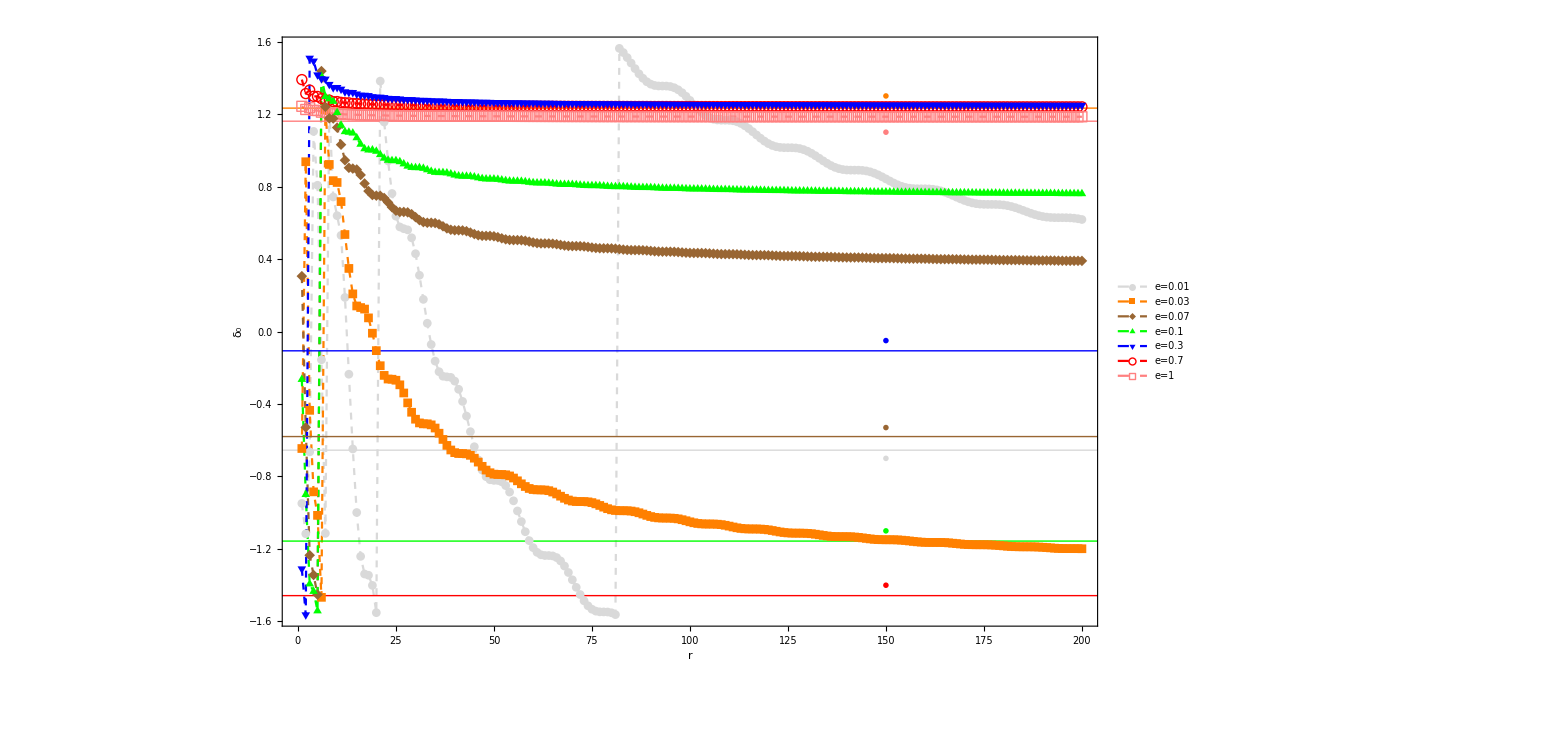

```mathematica
ListPlot[{SPS1,SPS2,SPS3,SPS4,SPS5,SPS6,SPS7},Frame->True,FrameTicks->{{All,None},{All,None}},Joined->True,PlotMarkers->Automatic,ImageSize->1200,FrameLabel->{"r","δ_0"},RotateLabel->False,PlotStyle->{{Dashed,LightGray,PointSize->Tiny},{Dashed,Orange,PointSize->Tiny},{Dashed,Brown,PointSize->Tiny},{Dashed,Green,PointSize->Tiny},{Dashed,Blue,PointSize->Tiny},{Dashed,Red,PointSize->Tiny},{Dashed,Pink,PointSize->Tiny}},Axes->None,Epilog->{{LightGray,Thin,InfiniteLine[{0,-0.654835316},{1,0}],Inset[Style["δ_0(e=0.01)=-0.654835316",14],{150,-0.7}]},{Orange,Thin,InfiniteLine[{0,1.232867297},{1,0}],Inset[Style["δ_0(e=0.03)=1.232867297",14],{150,1.3}]},{Brown,Thin,InfiniteLine[{0,-0.579619620},{1,0}],Inset[Style["δ_0(e=0.07)=-0.579619620",14],{150,-0.53}]},{Green,Thin,InfiniteLine[{0,-1.156444634},{1,0}],Inset[Style["δ_0(e=0.1)=-1.156444634",14],{150,-1.1}]},{Blue,Thin,InfiniteLine[{0,-0.106466466},{1,0}],Inset[Style["δ_0(e=0.3)=-0.106466466",14],{150,-0.05}]},{Red,Thin,InfiniteLine[{0,-1.457426179},{1,0}],Inset[Style["δ_0(e=0.7)=-1.457426179",14],{150,-1.4}]},{Pink,Thin,InfiniteLine[{0,1.160634967},{1,0}],Inset[Style["δ_0(e=1)=1.160634967",14],{150,1.1}]}},PlotLegends->{"e=0.01","e=0.03","e=0.07","e=0.1","e=0.3","e=0.7","e=1"}]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_PhaseShift_NA_Yukawa_1.eps",%];
```

```mathematica
Unset[e];
N[1/(2I)Log[Gamma[1-I/(√(2#))]/Gamma[1+I/(√(2#))]]]&/@{0.01,0.03,0.07,0.1,0.3,0.7,1}
```

{-1.25044+5.55112×10^-17 ⅈ,0.716281+5.55112×10^-17 ⅈ,-0.708782+0. ⅈ,-0.311203+5.55112×10^-17 ⅈ,0.242033-5.55112×10^-17 ⅈ,0.306557+0. ⅈ,0.293923+0. ⅈ}

```mathematica
{-0.654835316,1.232867297,-0.579619620,-1.156444634,-0.106466466,-1.457426179,1.160634967}
```

{-0.654835,1.23287,-0.57962,-1.15644,-0.106466,-1.45743,1.16063}

```mathematica
%1-%3
```

```mathematica
{0.5956066894816177-5.551115123125783*^-17 ⅈ,0.5165865057729152-5.551115123125783*^-17 ⅈ,0.1291623302503362+0. ⅈ,-0.8452418156010307-5.551115123125783*^-17 ⅈ,-0.34849924048046027+5.551115123125783*^-17 ⅈ,1.3776094345459944+0. ⅈ,0.8667124317575183+0. ⅈ}
```

{0.595607-5.55112×10^-17 ⅈ,0.516587-5.55112×10^-17 ⅈ,0.129162+0. ⅈ,-0.845242-5.55112×10^-17 ⅈ,-0.348499+5.55112×10^-17 ⅈ,1.37761+0. ⅈ,0.866712+0. ⅈ}

```mathematica
-1.7639832190437987 +π
```

1.37761